```mathematica
len = 22;
f = Table[Number, {i, 1, len}];
```

```mathematica
l = ReadList["total-routes-sparse.txt", f];
```

```mathematica
Tally[Table[l[[i]][[1]], {i, 1, Length[l]}]]
```

{{0,33187},{3,5236},{1,9125},{5,10738},{9,10336},{4,1175},{21,89},{11,369},{15,988},{18,228},{10,233},{13,1171},{16,1268},{20,345},{6,2624},{2,540},{7,249},{8,123},{12,713},{14,841},{17,18},{19,394}}

```mathematica
c=Tally[l];
```

```mathematica
sortc=SortBy[c,Last];
```

```mathematica
(* n = 70 for original *)
```

```mathematica
n =80;
```

```mathematica
top=Table[sortc[[-i]], {i, 1, n}];
```

```mathematica
str = str0 = str1="";
For[i=1,i≤len, i++, str1 = str1<>"1"];
For[i=1,i≤len, i++, str0 = str0<>"0"];
str = str0;
```

```mathematica
gt = {};
For[i=1,i≤Length[top],i++,
state = str;
For[j=1,j≤len,j++,
s = Characters[state];
s[[top[[i]][[1]][[j]]+1]] = "1";
newstate = StringJoin[s];
AppendTo[gt,Table[{state,newstate}, {k, 1, top[[i]][[2]]}]];
state = newstate;
];
];
```

```mathematica
gt = Flatten[gt,1];
```

```mathematica
gtu = Union[gt];
```

```mathematica
g = Table[{gtu[[i]][[1]]->gtu[[i]][[2]], Length[Position[gt,gtu[[i]]]]}, {i, 1, Length[gtu]}];
```

```mathematica
gprime ={};
For[i=1,i≤Length[g],i++,
If[g[[i]][[2]] > 1, AppendTo[gprime, g[[i]]]];
];
```

```mathematica
gprime = g;
```

```mathematica
For[i=1,i<50,i++,
AppendTo[gprime, {ToString[3000000+i]->str0, 10}];
AppendTo[gprime, {ToString[2000000+i]->str1, 10}];
];
```

```mathematica
notables = {"1111111111111111111111","1111111111111111111111","1111111111111111111111","1111110111111111111111","1111111111101111111110","1111110111111111111100","1111101111101111111100","1111011101001111011000","1111101001100001010000","1100011110000001010000","0100010001010111100000","1111000000100110000000","0101010110001000000000","1000010011000000000000","1100001010000000000000","1000010100000000000000","1000011000000000000000","1110000000000000000000","1000100000000000000000","0101000000000000000000","1000000000000000000000","1000000000000000000000"};
```

```mathematica
names={"NW Monkeys", "Chimps", "Orangutans", "Bonobos", "Gorillas", "OW Monkeys", "Birds", "Elephants", "Carnivores", "Rodents", "Gibbons", "Insects", "Cetaceans", "Ungulates", "Cephalopods", "Prosimians", "Crustaceans", "Arachnids", "Gastropods", "Fish", "Amphibians", "Echinoids"};
```

```mathematica
fs = 15;
fs2 = 15;
```

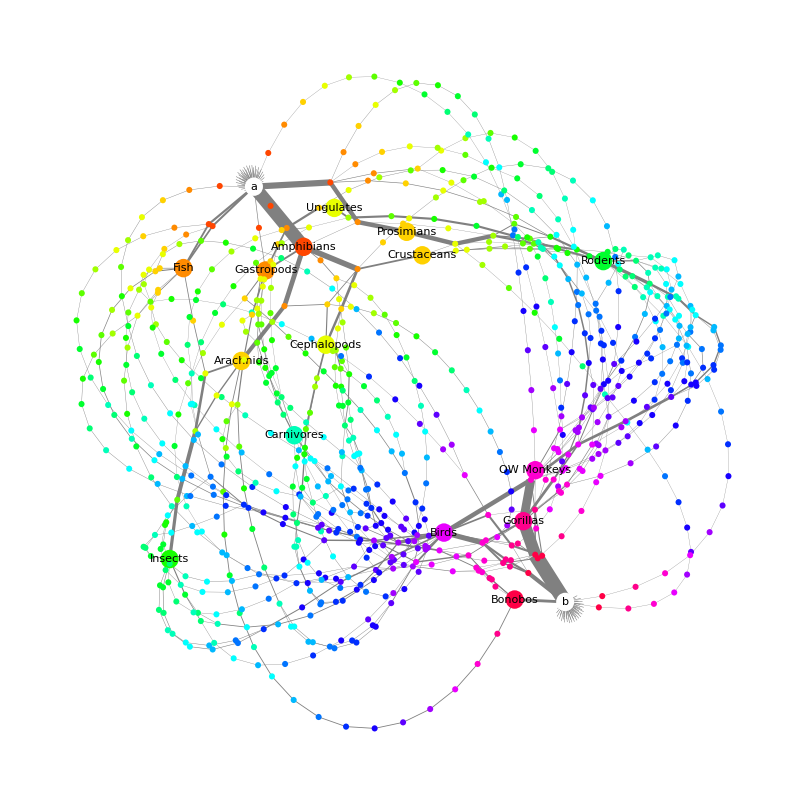

```mathematica
gplot=GraphPlot[gprime, VertexRenderingFunction->({If[StringTake[#2,{1}]≠ "2" &&StringTake[#2,{1}]≠ "3", {EdgeForm[],Hue[StringCount[#2,"1"]/22],If[#2==str1 ||#2==str0, White],If[#2==str1 ||#2==str0|| Length[Position[notables,#2]]≠ 0, Disk[#,0.3],Disk[#,0.1]], Black,If[#2==str1 , Style[Text["b", #1], FontSize->fs], If[#2==str0, Style[Text["a", #1],FontSize->fs], If[Length[Position[notables,#2]]≠ 0, Style[Text[names[[Flatten[Position[notables,#2]]]][[1]], #1], FontSize->fs2]]] ]}]}&),EdgeRenderingFunction->({Gray,Thickness[5*#3/10^5], Line[#1]}&) , AspectRatio->1]
```

```mathematica
Export["flower3new.svg", gplot, ImageSize->640]
```

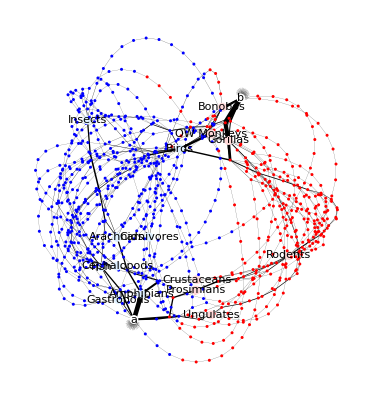

```mathematica
gplot=GraphPlot[gprime, VertexRenderingFunction->({If[StringTake[#2,{1}]≠ "2" &&StringTake[#2,{1}]≠ "3", {EdgeForm[],If[StringTake[#2,{6}]=="1", If[Length[Position[notables,#2]]≠ 0, LightRed,Red], If[Length[Position[notables,#2]]≠ 0, LightBlue,Blue]],If[#2==str1 ||#2==str0, White],If[#2==str1 ||#2==str0|| Length[Position[notables,#2]]≠ 0, Disk[#,0.3],Disk[#,0.1]], Black,If[#2==str1 , Text["b", #1], If[#2==str0, Text["a", #1], If[Length[Position[notables,#2]]≠ 0, Text[names[[Flatten[Position[notables,#2]]]][[1]], #1]]]] }]}&),EdgeRenderingFunction->({Thickness[3*#3/10^5], Line[#1]}&) ]
```

```mathematica
modes = {"Affix", "Throw", "Bait", "Contain", "Pry", "Wave-shake", "Block", "Prop-climb", "Dig", "Scratch", "Pound", "Hang", "Wipe", "Insert-probe", "Drop", "Reach", "Absorb", "Drag-roll", "Club", "Jab-stab", "Symbolize", "Cut"};
```

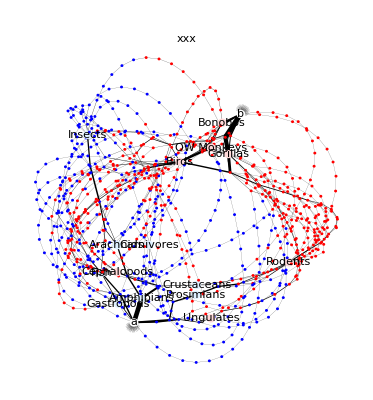

```mathematica
gplot=GraphPlot[gprime, VertexRenderingFunction->({If[StringTake[#2,{1}]≠ "2" &&StringTake[#2,{1}]≠ "3", {EdgeForm[],If[StringTake[#2,{9}]=="1", If[Length[Position[notables,#2]]≠ 0, LightRed,Red], If[Length[Position[notables,#2]]≠ 0, LightBlue,Blue]],If[#2==str1 ||#2==str0, White],If[#2==str1 ||#2==str0|| Length[Position[notables,#2]]≠ 0, Disk[#,0.3],Disk[#,0.1]], Black,If[#2==str1 , Text["b", #1], If[#2==str0, Text["a", #1], If[Length[Position[notables,#2]]≠ 0, Text[names[[Flatten[Position[notables,#2]]]][[1]], #1]]]] }]}&),EdgeRenderingFunction->({Thickness[3*#3/10^5], Line[#1]}&) , PlotLabel->"xxx"]
```

```mathematica
gplottab=GraphicsGrid[Table[Table[gplot=GraphPlot[gprime, VertexRenderingFunction->({If[StringTake[#2,{1}]≠ "2" &&StringTake[#2,{1}]≠ "3", {EdgeForm[],If[StringTake[#2,{4*(i-1)+j}]=="1", If[Length[Position[notables,#2]]≠ 0, LightRed,Red], If[Length[Position[notables,#2]]≠ 0, LightBlue,Blue]],If[#2==str1 ||#2==str0, White],If[#2==str1 ||#2==str0|| Length[Position[notables,#2]]≠ 0, Disk[#,0.3],Disk[#,0.1]], Black,If[#2==str1 , Text["b", #1], If[#2==str0, Text["a", #1], If[Length[Position[notables,#2]]≠ 0, Text[names[[Flatten[Position[notables,#2]]]][[1]], #1]]]] }]}&),EdgeRenderingFunction->({Thickness[3*#3/10^5], Line[#1]}&), PlotLabel->modes[[4*(i-1)+j]] ],{j, 1,4}],  {i, 1, 5}]];
```

```mathematica
Export["allflowers3new.png", gplottab, ImageSize->3000]
```